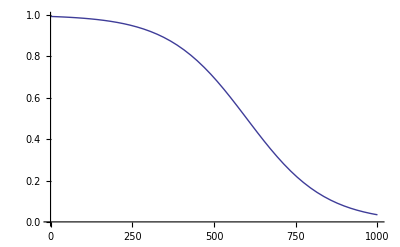

```mathematica
f[x_]:=1-1/(1+Exp[-(x-600)/120]);
Plot[f[x],{x,0,1000}]
```

```mathematica
f[x_,y_]:=1/3 1/0.5 Exp[-x/3]Exp[-y/0.5];
Integrate[Integrate[f[x,y],{y,0,2-x}],{x,0,2}]
```

0.387563

```mathematica
-1/3(Exp[-4] 3/5(Exp[10/3]-1)+3(Exp[-2/3]-1))//N
```

0.387563